## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[4];
```

## Utility Functions

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a,b,h}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a-m*h,b,h}]//N;

Return[xs];
]
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kh},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kh = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kh}]];
];
```

```mathematica
yvec[k_,p_]:=Module[{n,m, h,cDiffCoeffs,numNonzero, nonZeroElements},
n=p["n"];
m=p["m"];
h = p["h"];

cDiffCoeffs={1,-2,1};

nonZeroElements={
n+m->-cDiffCoeffs[[1]],
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]+2*h^2*k^2)
};

Return[SparseArray[nonZeroElements,{n+m+1}]];
]
```

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{n,m,cDiffCoeffs,bands},
n=p["n"];
m=p["m"];

cDiffCoeffs={1,-2,1};

bands=Table[Band[{1,i}]->cDiffCoeffs[[i]],{i,1,Length[cDiffCoeffs]}];

Return[SparseArray[bands,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ n,m, h, band},
n=p["n"];
m=p["m"];
h = p["h"];

(*band = Band[{1,3}]->2*h^2*k^2;*)
band = Band[{1,2}]->2*h^2*k^2;
Return[SparseArray[band,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,Vparams_,SEDict_]:=Module[{xg,n,m, h, u1V, matV},
xg=xgrid[SEDict][[2;;-1]];
n=SEDict["n"];
m=SEDict["m"];
h =SEDict["h"];

u1V=Band[{m+1,m+2}]->2*h^2*V[xg,Vparams];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

## Solve Schrodinger equation

```mathematica
SchrEqOfV[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,VParams, SEDict];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]],Method->"Banded"]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
TofV[k_,x1_,x2_,SEsol1_,SEsol2_]:=Module[{},
Exp[I*Sqrt[2]*k*x2]*(1-Exp[-I*2*Sqrt[2]*k*(x2-x1)])/
(SEsol2-SEsol1*Exp[-I*Sqrt[2]*k*(x2-x1)])
];
```

```mathematica
TofVVec[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=
Module[{step,solk,xgf,x1,x2,Tk},
step=SEDict["TCalcStep"];
solk=SchrEqOfV[V,VParams,SEDict,kVec,D2,EMatrixVector,yVector];
xgf=xgridFull[SEDict];
x1=xgf[[1]];
x2=xgf[[step]];

Tk=Table[{
sol[[1]], 
TofV[sol[[1]],x1,x2, sol[[2,1]],sol[[2,step]]]
},
{sol,solk}];

Return[Tk];
]
```

## Define Cost Function

```mathematica
Cost[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},

(*Calculate the cost function*)
cost = Sum[
weights[[i]]*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}] /
 Sum[weights[[i]],{i,1,Length[T]}] ;
Return[cost];
];
```

```mathematica
CostTemp[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},
temp=SEDict["temp"];

(*Calculate the cost function*)
cost = Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi))*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}]/
Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi)),{i,1,Length[T]}] ;

Return[cost];
];
```

```mathematica
CostConstraint[ErrFunc_, Vpars_,SEDict_]:=Module[{alpha},
alpha=SEDict["alpha"];
alpha * ErrFunc[Vpars,SEDict]
]
```

## Search for the potential

```mathematica
BackgroundWeights[k_]:=Sqrt[Sinh[Pi Sqrt[2]k]^2/(Sinh[Pi Sqrt[2]k]^2+Cosh[Pi Sqrt[7]/2]^2)]
```

```mathematica
CustomStepMonitor[TGoal_,Vfunc_,Vpars_,SEDict_,kVec_ ,costFunction_,d2_,eMatrix_,yvec_,weights_:Table[1,{i,1,Length[TGoal_]}]]:=
Module[{tvec,cost,PlotA,PlotB},
tvec=TofVVec[Vfunc, Vpars,SEDict,kVec,d2,eMatrix,yvec];
cost=costFunction[Abs[tvec], TGoal, SEDict,weights];

(*ALERT: very bad programming!!!*)
If[cost≠lastCost,
Print["Cost: ", cost];
Print["Params: ",Vpars]; 

PlotA=Plot[Vfunc[x,Vpars],{x,SEDict["a"],SEDict["b"]},PlotRange->All];
PlotB=ListPlot[{TGoal,Abs[tvec]},PlotRange->All,PlotLabel->"Cost: "<>ToString[cost], Joined->True];

Print[GraphicsRow[{PlotA,PlotB}, ImageSize->Large]]
];

lastCost=cost;
]
```

```mathematica
SearchPotential [
TGoal_,Vfunc_,Vpars_,parConstrs_,SEDict_,kVec_, costFunction_,errFunction_,
weights_:Table[1,{i,1,Length[TGoal_]}],
method_:{
"DifferentialEvolution", 
"Tolerance"->0.1,
"PostProcess"->False,
"PenaltyFunction"->Function[{d,i},d*10^(2)], 
"ScalingFactor"->0.75,
 "CrossProbability"->0.5,
"RandomSeed"->3
}
]:=
Module[{VparsFlat, soln,d2mat,emat,yyvec,lastCost},
VparsFlat=Flatten[Vpars];
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

lastCost=1000;

soln=NMinimize[{
Hold[
costFunction[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec]], TGoal,SEDict,weights]+
CostConstraint[errFunction, Vpars,SEDict]
],
parConstrs
},
VparsFlat, 
Method->method, 
AccuracyGoal->2,
PrecisionGoal->2,
MaxIterations->500,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,costFunction,d2mat,emat,yyvec,weights]]]
];

Return[soln];
]
```

## Define potentials

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma^2];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

```mathematica
VGaussL2Err[params_,SEDict_]:=Module[{pot,A,x0,σ,a,b,Vout},
A=params[[1]];
x0=params[[2]];
σ=params[[3]];
a=SEDict["a"];
b=SEDict["b"];

Vout=√(π/2) A √σ (Erfc[(-a+x0)/(√2 √σ)]+Erfc[(b-x0)/(√2 √σ)]);

Return[Abs[Vout]^2];
];
```

```mathematica
VGaussL2ErrN[params_,SEDict_]:=Module[{pot},
pot=Sum[VGaussL2Err[pars,SEDict],{pars,params}];
Return[pot];
];
```

## Main Section Examples

## “k=1 single-comb” 3 gaussians

### Define all inputs:

#### Solve parameters

```mathematica
SEDict = Association["a"->-10, "b"->10,"n"->1000,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->200, "TCalcStep"->25, "temp"->0.5, "alpha"->30];
SEDict["h"]=(SEDict["b"]-SEDict["a"])/SEDict["n"];
kgrid = kGrid[SEDict];
```

#### T target

```mathematica
TFunc[k_,a_,b_]:=(1+(k-a)^2/b^2)^(-1)
```

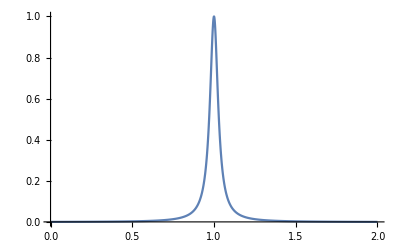

```mathematica
a=1;b=0.03;
Plot[TFunc[k,a,b],{k,0,2}, PlotRange->Full]
```

```mathematica
TTarget=Table[{k,TFunc[k,a,b]},{k,kgrid}];
```

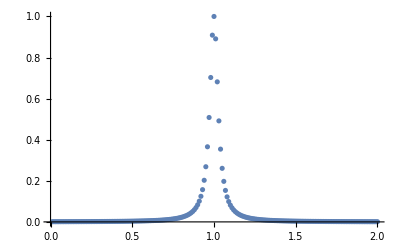

```mathematica
ListPlot[TTarget,PlotRange->Full]
```

#### k weights:

```mathematica
kWeightsFunc[r_]:=Module[{wts,norm},
wts=Table[BackgroundWeights[k]+r*TFunc[k,a,b],{k,kgrid}];
norm=Total[wts];
Return[wts/norm];
]
```

```mathematica
kWeights=kWeightsFunc[2];
kWeightsTooWeak =kWeightsFunc[1];
kWeightsTooStrong=kWeightsFunc[3];
```

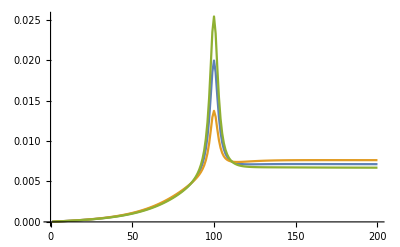

```mathematica
ListPlot[Evaluate[{kWeights,kWeightsTooWeak,kWeightsTooStrong}],PlotRange->All, Joined->True]
```

#### Constraints

```mathematica
pars=Hold[{
{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3}}]
```

Hold[{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}}]

```mathematica
constraints=Hold[{
sigma1>0.3,
sigma2>0.3, 
sigma3>0.3,
A1>-30,
A1<30,
A2>-30,
A2<30,
A2>-30,
A2<30,
x01+x02+x03==0
}]
```

Hold[{sigma1>0.3,sigma2>0.3,sigma3>0.3,A1>-30,A1<30,A2>-30,A2<30,A2>-30,A2<30,x01+x02+x03==0}]

### Minimize

Cost: 0.0767358

Params: {{-6.69144,0.0525527,1.48004},{29.9021,-0.488402,0.393571},{0.490569,0.435849,1.88641}}

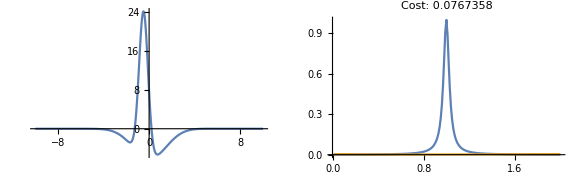

Cost: 0.0756134

Params: {{27.9091,1.16226,0.329027},{-10.5463,-0.652609,1.65782},{0.802252,-0.509647,0.833376}}

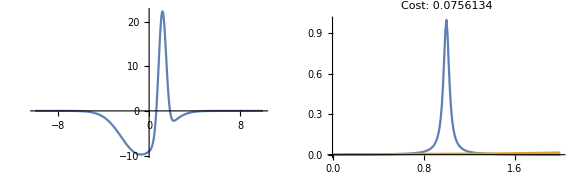

Cost: 0.070239

Params: {{-19.0418,0.286253,0.939912},{29.9806,0.136522,0.404981},{0.581994,-0.422775,1.19808}}

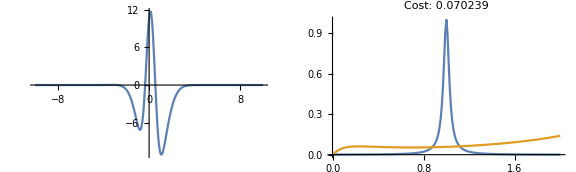

Cost: 0.069677

Params: {{-19.0418,0.918842,2.54558},{29.9806,0.136522,0.404981},{0.581994,-1.05536,1.57189}}

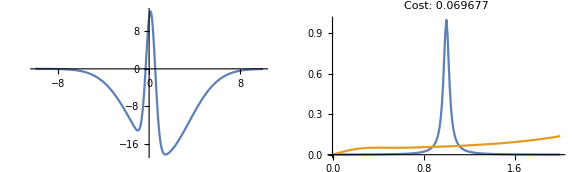

Cost: 0.0660409

Params: {{-16.4537,0.416341,0.422047},{20.282,0.859126,0.385245},{1.53496,-1.27547,0.346197}}

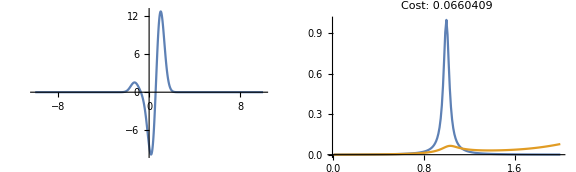

Cost: 0.0636176

Params: {{15.5793,1.2576,0.300313},{-29.99,0.319395,0.300862},{2.41248,-1.57699,0.304946}}

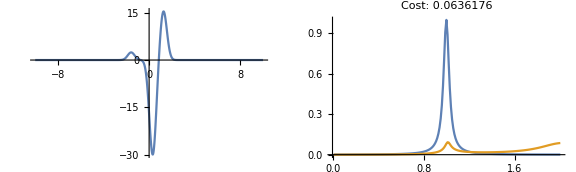

Cost: 0.0579676

Params: {{29.9999,-0.0907525,0.305448},{-29.9992,-0.738613,0.682},{1.05367,0.829365,1.45729}}

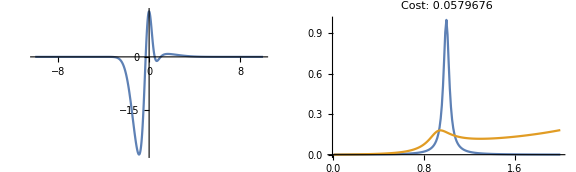

Cost: 0.0567183

Params: {{30.,-2.69713,0.3},{-30.,-1.23212,1.25161},{5.93338,3.92924,0.308655}}

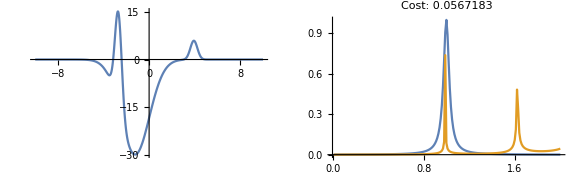

Cost: 0.0547862

Params: {{30.,-1.84477,0.3},{-13.4112,0.419631,5.42504},{-5.78275,1.42514,4.4322}}

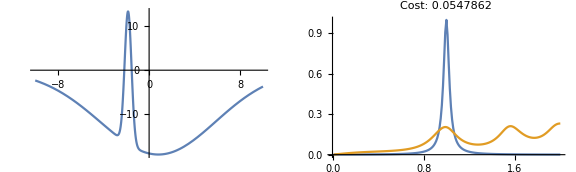

Cost: 0.0542694

Params: {{20.3245,-1.04349,0.300088},{-8.66954,-0.524612,2.81635},{7.74374,1.5681,0.337814}}

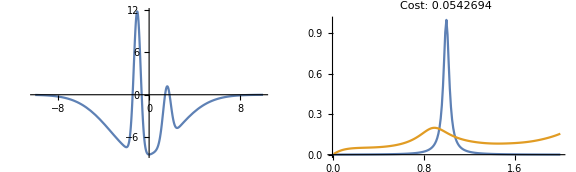

Cost: 0.042469

Params: {{13.0277,-1.04349,0.3},{-8.59601,-0.524612,2.81635},{13.4273,1.5681,0.3}}

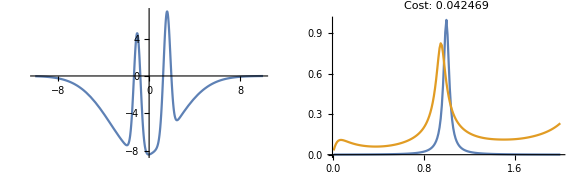

{0.042469,{A1→13.0277,x01→-1.04349,sigma1→0.3,A2→-8.59601,x02→-0.524612,sigma2→2.81635,A3→13.4273,x03→1.5681,sigma3→0.3}}

```mathematica
solGaussJustRight=
SearchPotential [
TTarget,
VGaussN,
ReleaseHold[pars],
ReleaseHold[constraints],
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
kWeights]
```

Cost: 0.0553399

Params: {{-18.8051,0.659213,1.12767},{26.4014,-0.720878,0.519782},{0.186866,0.0616653,1.23896}}

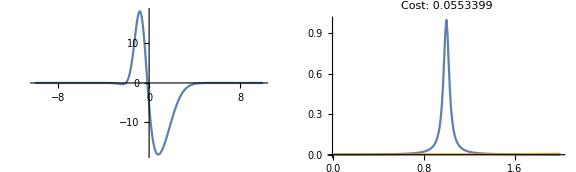

Cost: 0.0553136

Params: {{-6.69144,0.0525527,1.48004},{29.9021,-0.488402,0.393571},{0.490569,0.435849,1.88641}}

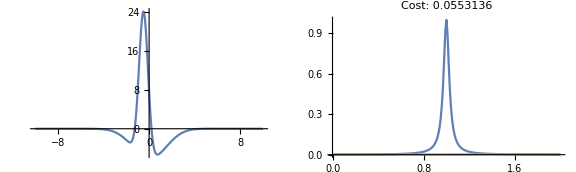

Cost: 0.0544729

Params: {{27.9091,1.16226,0.329027},{-10.5463,-0.652609,1.65782},{0.802252,-0.509647,0.833376}}

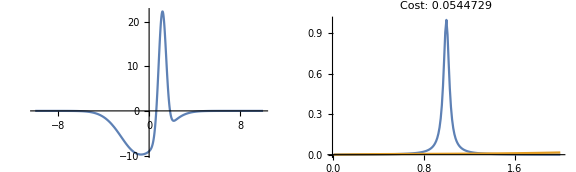

Cost: 0.0521786

Params: {{-19.0418,0.286253,0.939912},{29.9806,0.136522,0.404981},{0.581994,-0.422775,1.19808}}

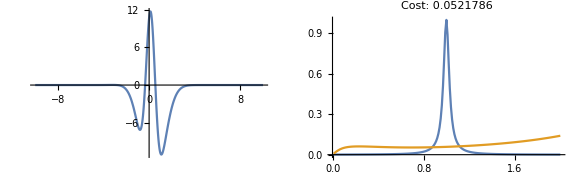

Cost: 0.0517748

Params: {{-19.0418,0.918842,2.54558},{29.9806,0.136522,0.404981},{0.581994,-1.05536,1.57189}}

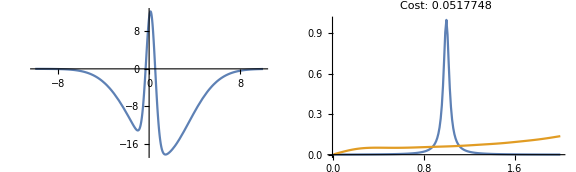

Cost: 0.0514644

Params: {{29.9981,-0.488666,0.355042},{-18.5211,0.387519,1.44318},{1.114,0.101147,1.43399}}

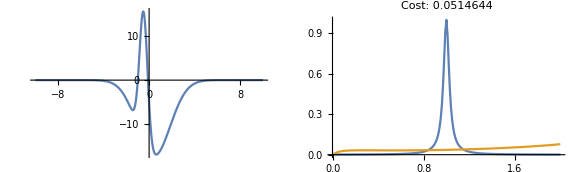

Cost: 0.0513461

Params: {{29.931,-0.640148,0.314965},{-26.3032,0.523827,1.16273},{-0.100193,0.116321,0.334563}}

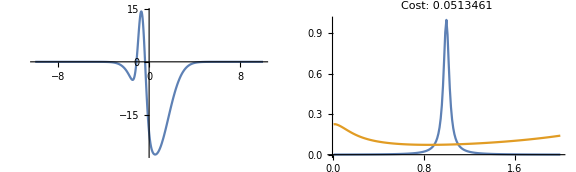

Cost: 0.0506477

Params: {{29.998,-0.945013,0.303459},{-29.9995,2.29862,2.18434},{-3.67264,-1.35361,3.04586}}

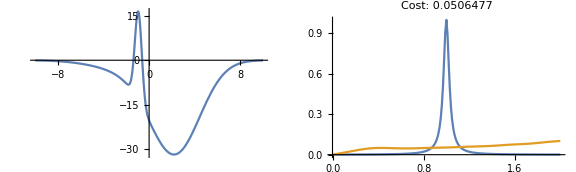

Cost: 0.0505708

Params: {{29.9997,0.806028,0.300522},{-11.8837,1.04682,0.928869},{0.715545,-1.85285,0.30044}}

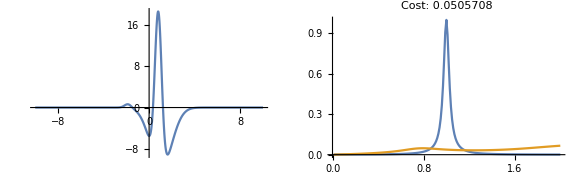

Cost: 0.0488422

Params: {{-30.,1.81996,3.97473},{29.9993,-3.01243,0.300403},{1.54257,1.19247,1.77686}}

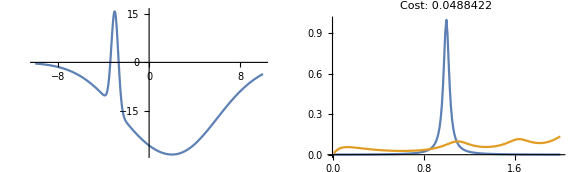

Cost: 0.0467525

Params: {{-30.,-2.58027,2.35699},{29.9993,-0.226005,0.300403},{1.54257,2.80628,2.94938}}

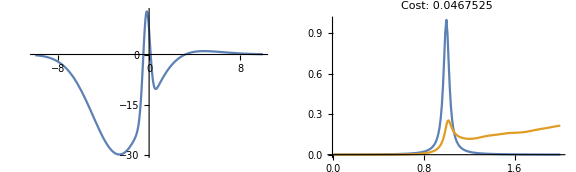

Cost: 0.0260045

Params: {{30.,-0.833379,0.303911},{-29.9912,-0.355333,0.570455},{7.15882,1.18871,0.450657}}

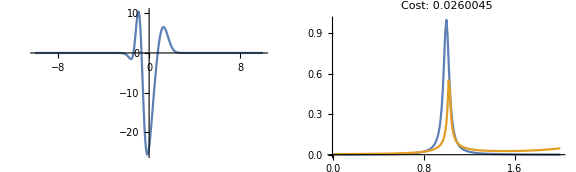

Cost: 0.0246601

Params: {{30.,-0.833379,0.303911},{-30.,-0.355333,0.570455},{7.15882,1.18871,0.450657}}

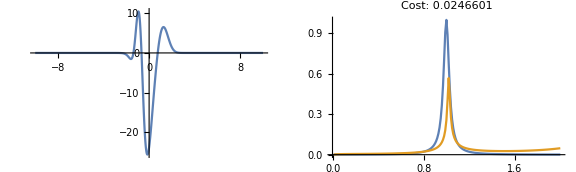

{0.0246601,{A1→30.,x01→-0.833379,sigma1→0.303911,A2→-30.,x02→-0.355333,sigma2→0.570455,A3→7.15882,x03→1.18871,sigma3→0.450657}}

```mathematica
solGaussNTooWeak=
SearchPotential [
TTarget,
VGaussN,
ReleaseHold[pars],
ReleaseHold[constraints],
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
kWeightsTooWeak]
```

Cost: 0.0955529

Params: {{-18.8051,0.659213,1.12767},{26.4014,-0.720878,0.519782},{0.186866,0.0616653,1.23896}}

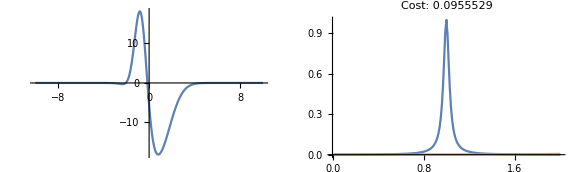

Cost: 0.0955119

Params: {{-6.69144,0.0525527,1.48004},{29.9021,-0.488402,0.393571},{0.490569,0.435849,1.88641}}

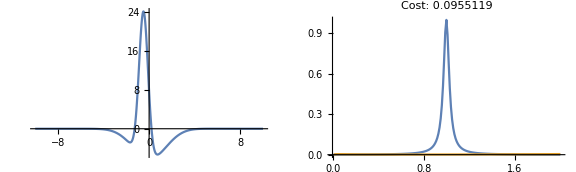

Cost: 0.0887509

Params: {{29.9979,-0.562413,0.561831},{-29.9943,0.94928,1.83952},{1.08785,-0.386867,1.61254}}

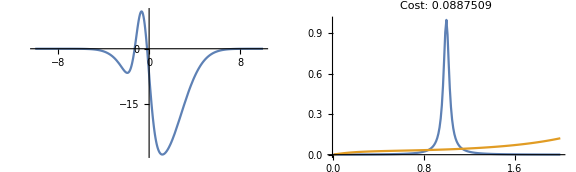

Cost: 0.0876601

Params: {{16.9741,-0.56151,0.333002},{-12.8982,0.921629,1.5793},{0.959422,-0.360119,0.346197}}

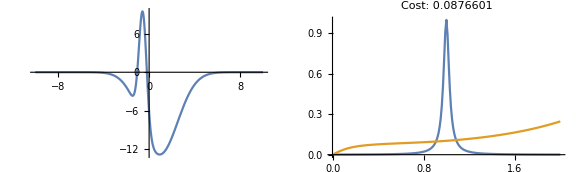

Cost: 0.0872722

Params: {{-29.9572,0.605561,1.68941},{29.9312,-0.720878,0.519782},{1.01963,0.115317,1.23896}}

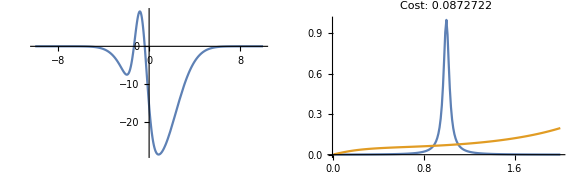

Cost: 0.086744

Params: {{-12.5243,1.11279,0.829316},{17.1507,-0.0838435,0.303137},{-0.298509,-1.02895,1.51213}}

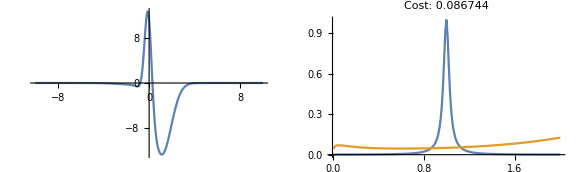

Cost: 0.0862872

Params: {{14.6459,0.511553,0.302131},{-14.9128,-0.766322,0.596136},{-1.45016,0.254769,0.932178}}

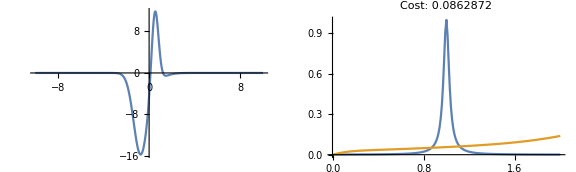

Cost: 0.0852446

Params: {{-10.6904,1.41948,1.66545},{23.7242,1.01185,0.306946},{0.265837,-2.43133,0.431256}}

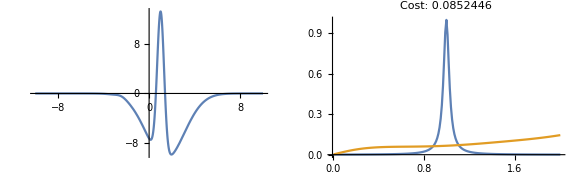

Cost: 0.082404

Params: {{29.9763,-1.75981,0.30273},{-23.1297,0.803931,2.8798},{0.577724,0.955878,0.313027}}

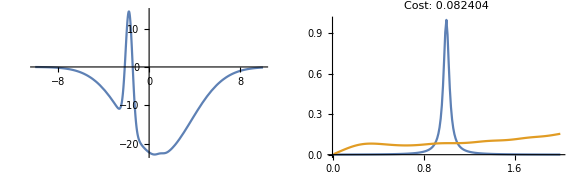

Cost: 0.08238

Params: {{-29.9995,-0.356908,0.300076},{29.9999,-0.0501521,0.300136},{-1.88769,0.40706,1.17652}}

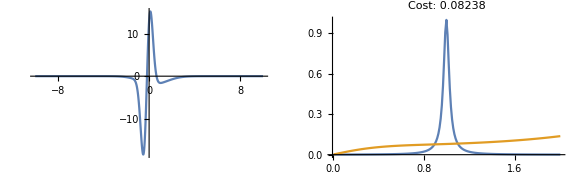

Cost: 0.0822931

Params: {{-29.9995,-0.356908,0.300076},{29.9999,-0.0501521,0.300136},{-1.88769,0.40706,1.07017}}

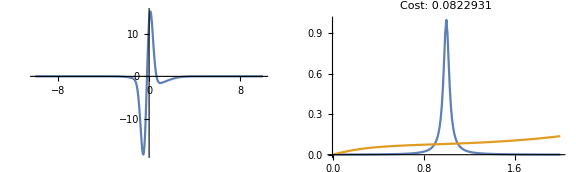

Cost: 0.0822546

Params: {{-29.9995,-2.25574,1.73454},{29.9999,-0.0501521,0.300136},{-1.88769,2.30589,4.13676}}

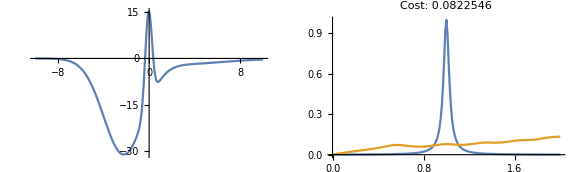

Cost: 0.0778901

Params: {{30.,1.75484,0.300731},{-30.,-1.90299,3.26516},{-0.672925,0.148148,0.367175}}

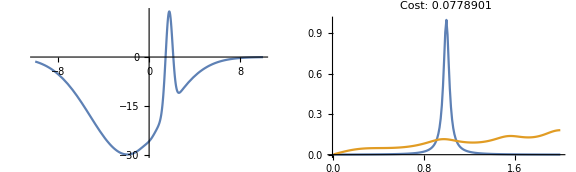

Cost: 0.0778145

Params: {{30.,1.75484,0.3},{-30.,-1.90299,3.26516},{-0.672925,0.148148,0.3}}

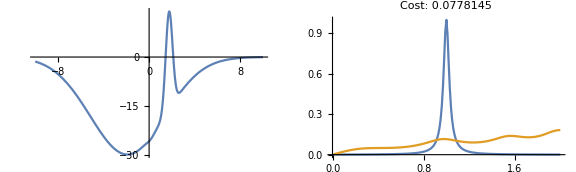

Cost: 0.076544

Params: {{28.116,0.086883,0.300529},{-14.769,-1.57139,4.59012},{2.58429,1.48451,0.314947}}

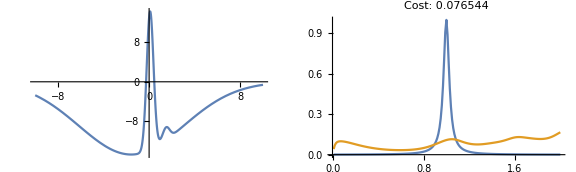

Cost: 0.0735289

Params: {{-30.,-1.49292,0.30012},{30.,-1.67982,0.3},{2.46827,3.17274,0.3}}

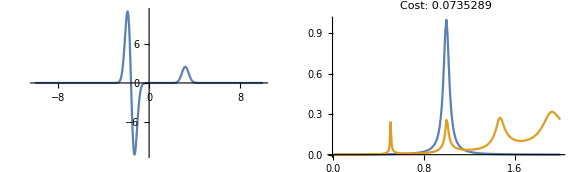

Cost: 0.0667113

Params: {{30.,2.95435,0.3},{-29.9999,-1.65059,4.30828},{-3.79979,-1.30376,0.966671}}

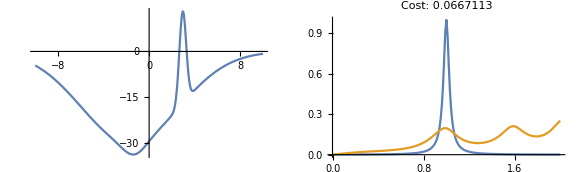

$Aborted

```mathematica
solGaussNTooStrong=
SearchPotential [
TTarget,
VGaussN,
ReleaseHold[pars],
ReleaseHold[constraints],
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
kWeightsTooStrong]
```

## Error Estimation

The goal is to understand how errors in the potential parameters will effect the T-profile.

```mathematica
(*A function to get the T profile for a specified potential*)
GetTVec[
TGoal_,Vfunc_,Vpars_,SEDict_,kVec_
]:=
Module[{d2mat,emat,yyvec, result},
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

result=TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec];

Return[result]
]
```